```mathematica
Integrate[-eF x √(2/a) Sin[(m π)/a x] √(2/a)Cos[π/a x] ,{x,-a/2,a/2}]
```

(2 a eF (4 m Cos[(m π)/2]+(-1+m^2) π Sin[(m π)/2]))/((-1+m^2)^2 π^2)

```mathematica
Integrate[-eF x √(2/a) Cos[(m π)/a x] √(2/a)Sin[π/a x] ,{x,-a/2,a/2}]
```

-(2 a eF (2 (1+m^2) Cos[(m π)/2]+m (-1+m^2) π Sin[(m π)/2]))/((-1+m)^2 (1+m)^2 π^2)

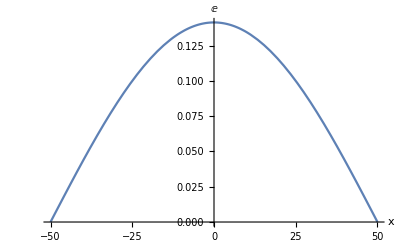

```mathematica
psi1 = Plot[√(2/100) Cos[(π x)/100], {x, -50, 50}, AxesLabel ->{x, E}]
```

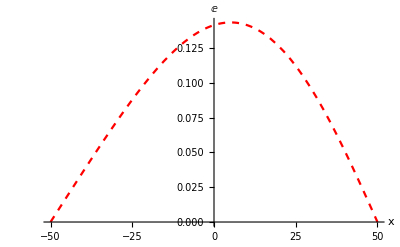

```mathematica
psi2 = Plot[√(2/100) Cos[(π x)/100]+16/π^4(2/((2^2-1)^3)Sin[(2π x)/100]-4/((4^2-1)^3) Sin[(4π x)/100] + 6/((6^2-1)^3) Sin[(6π x)/100]),  {x, -50, 50}, PlotStyle->{Dashed, Red}, AxesLabel ->{x, E}]
```

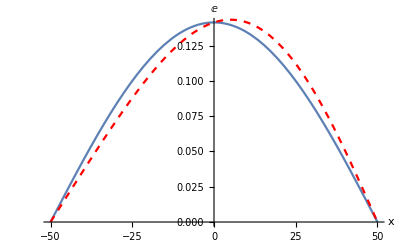

```mathematica
Show[psi1, psi2]
```